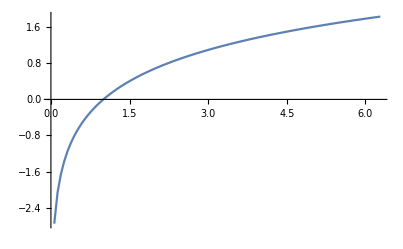

```mathematica
f[x_]:=Log[x];g[x_]:=Sin[x];h[x_]:=Sqrt[x]
Np=100;Ni=Np-1;dx=2Pi/Ni;
xv=Table[i,{i,0,2Pi,dx}];
fxv=Table[{xv[[i]],f[xv[[i]]]},{i,1,Np}];
ListLinePlot[fxv]
```